```mathematica
S={{0,1,0},{-1,0,1},{0,-1,0}};
%//MatrixForm
```

(0 | 1 | 0
-1 | 0 | 1
0 | -1 | 0)

```mathematica
S.S//MatrixForm
S.S.S//MatrixForm
```

(-1 | 0 | 1
0 | -2 | 0
1 | 0 | -1)

(0 | -2 | 0
2 | 0 | -2
0 | 2 | 0)

```mathematica
Cos[S/(I √2)]//MatrixForm
```

(1 | Cosh[1/(√2)] | 1
Cosh[1/(√2)] | 1 | Cosh[1/(√2)]
1 | Cosh[1/(√2)] | 1)

```mathematica
Sin[S/(I √2)]//MatrixForm
```

(0 | -ⅈ Sinh[1/(√2)] | 0
ⅈ Sinh[1/(√2)] | 0 | -ⅈ Sinh[1/(√2)]
0 | ⅈ Sinh[1/(√2)] | 0)

```mathematica
Exp[θ S/√2]//MatrixForm
```

(1 | ⅇ^(θ/(√2)) | 1
ⅇ^(-θ/(√2)) | 1 | ⅇ^(θ/(√2))
1 | ⅇ^(-θ/(√2)) | 1)

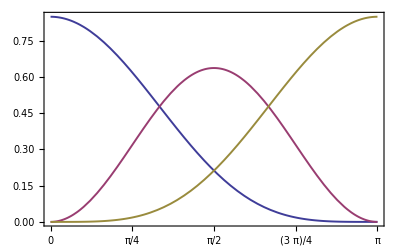

```mathematica
Plot[{8/(3 π)(1+Cos[θ])^2/4,4/π(Sin[θ])^2/2,8/(3 π)(1-Cos[θ])^2/4},
{θ,0,π},PlotStyle->{Thickness[0.0035]},
Frame->{{True,True},{True,False}},
FrameTicks->{{Automatic,Automatic},{{0,π/4,π/2,3π/4,π},None}},
PlotRange->{{0,π},{0,0.85}}
]
```

```mathematica
Export["plot.pdf",%4,"PDF"]
```

plot.pdf

```mathematica
Integrate[8/(3 π)(1+Cos[θ])^2/4,{θ,0,π}]
```

1

```mathematica
Integrate[4/π(Sin[θ])^2/2,{θ,0,π}]
```

1